a[tmax]: 3.99999859848042

b[tmax]: 4.000001382550143

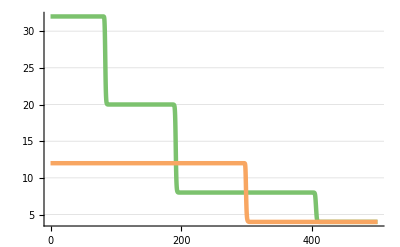

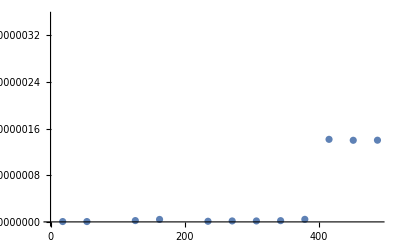

```mathematica
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsys[32,12];
tmax=500;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
Print["a[tmax]: " <> ToString[r0tmax]];
Print["b[tmax]: " <> ToString[r1tmax]];
PlotForPaper[Evaluate[{a[t],b[t]}/.sol], tmax]
(*Plot[Evaluate[{a[t],b[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{Magenta, Orange},Ticks->{Range[0,tmax,100],Automatic}]*)
errorMap=EvaluateError[rsys, tmax];
aErrorList=errorMap[a]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[aErrorList,Ticks->{Range[0,tmax,100],Automatic}]
```

a[tmax]: 3.999991614437524

b[tmax]: 3.999987498570831

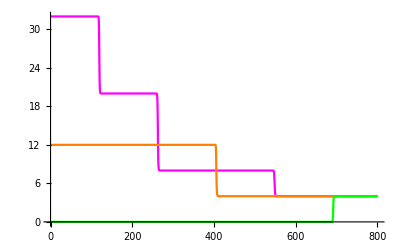

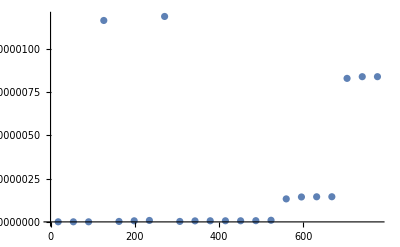

```mathematica
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsysWithOutput[32,12];
tmax=800;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
Print["a[tmax]: " <> ToString[r0tmax]];
Print["b[tmax]: " <> ToString[r1tmax]];
Plot[Evaluate[{a[t],b[t],out[t]}/.sol],{t,0,tmax},PlotRange->{0,All},PlotStyle->{Magenta, Orange, Green},Ticks->{Range[0,tmax,100],Automatic}]
errorMap=EvaluateError[rsys, tmax];
aErrorList=errorMap[a]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[aErrorList,Ticks->{Range[0,tmax,100],Automatic}]
```

a[tmax]: 5.243155784528075

b[tmax]: 84.7675107651017

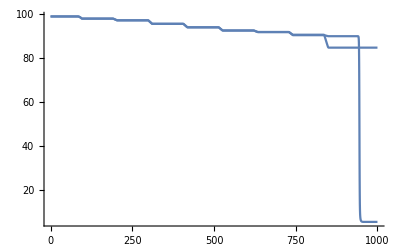

lt1: 0.494722 lt2: 0.494722

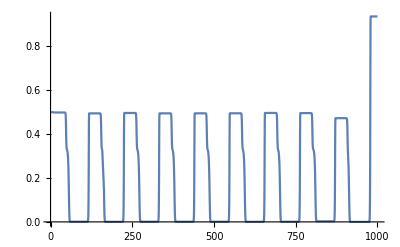

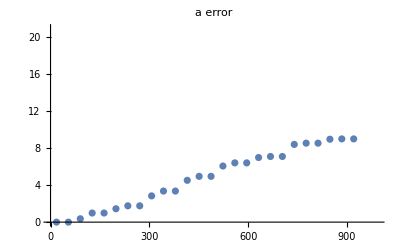

```mathematica
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsys[99,99];
tmax=1000;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
Print["a[tmax]: " <> ToString[r0tmax]];
Print["b[tmax]: " <> ToString[r1tmax]];
Plot[{a[t],b[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
lt1=DecimalForm[EvaluateRxnAtPoint[sol,xlty,150]];
lt2=DecimalForm[EvaluateRxnAtPoint[sol,yltx,150]];
Print["lt1: " <> ToString[lt1] <> " lt2: " <> ToString[lt2]];
Plot[{xlty[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
errorMap=EvaluateError[rsys, tmax];
aErrorList=errorMap[a]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[aErrorList,Ticks->{Range[0,tmax,100],Automatic},PlotLabel->"a error"]
```

a[tmax]: 98.5577005018527

b[tmax]: 98.5577004872956

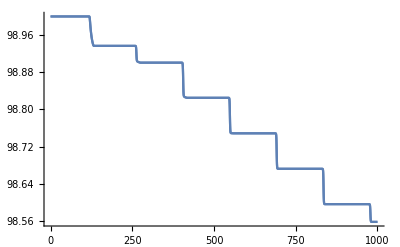

lt1: 0.0007672034771942629 lt2: 0.0007672035500982171

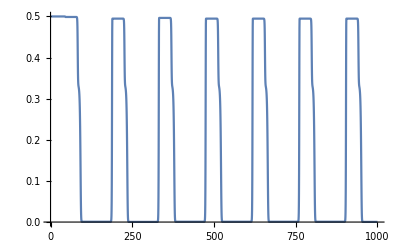

```mathematica
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsysErrorCorrecting[99,99];
tmax=1000;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
Print["a[tmax]: " <> ToString[r0tmax]];
Print["b[tmax]: " <> ToString[r1tmax]];
Plot[{a[t],b[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
lt1=NumberForm[EvaluateRxnAtPoint[sol,xlty,150],Infinity];
lt2=NumberForm[EvaluateRxnAtPoint[sol,yltx,150],Infinity];
Print["lt1: " <> ToString[lt1] <> " lt2: " <> ToString[lt2]];
Plot[{xlty[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
```

r0[tmax]: 0.581351634612921

r1[tmax]: 0.05525765417081837

out[tmax]: 98.9999999729831

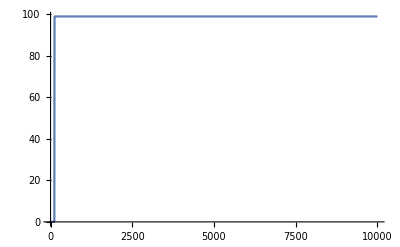

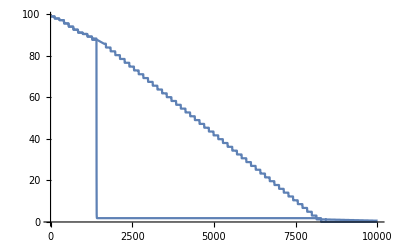

```mathematica
Get[NotebookDirectory[]<>"/gcd.m"]

rsys=GCDRsysWithOutput[99,99];
tmax=10000;
sol=SimulateRxnsys[ExpandDiscreteRsys[rsys], tmax];
r0tmax=NumberForm[EvaluateRxnAtPoint[sol,a,tmax], Infinity];
r1tmax=NumberForm[EvaluateRxnAtPoint[sol,b,tmax], Infinity];
outmax=NumberForm[EvaluateRxnAtPoint[sol,out,tmax], Infinity];
Print["r0[tmax]: " <> ToString[r0tmax]];
Print["r1[tmax]: " <> ToString[r1tmax]];
Print["out[tmax]: " <> ToString[outmax]];
Plot[{out[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
Plot[{a[t],b[t]}/.sol,{t,0,tmax},PlotRange->{0,All}]
```